```mathematica
myexpr2[10,0.1,0.1,0.001]
```

$Aborted

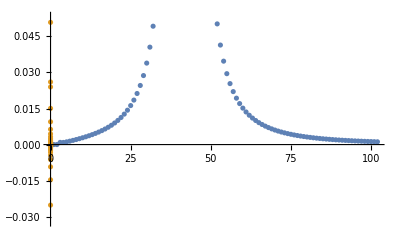

```mathematica
tmp = (β Exp[β(ϵ-μ)])/(1+Exp[β(ϵ-μ)])^2(π^2 α^2 ϵ^2 (2 ϵ^2-3 λ^2)+4 λ^2 (ϵ^2-2 λ^2))/(2 (ϵ-λ) (λ+ϵ) (π^2 α^2 ϵ^2+4 λ^2));
residues = Join[{λ,-λ},Table[μ+(ⅈ π (2 n+1))/β,{n,1,100}]];
tmp=Table[ⅈ π Residue[tmp,{ϵ,ϵp}]//Simplify,{ϵp,residues}]/.nsubst;
Transpose[{Table[n,{n,1,102}],tmp}];
ListPlot[Evaluate[%//{Re[#],Im[#]}&]]
```

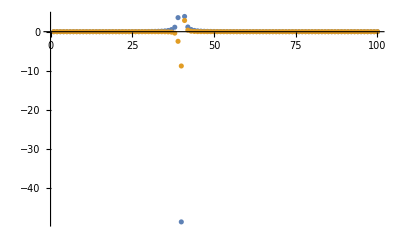

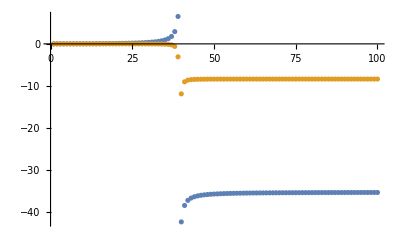

```mathematica
ListPlot[Evaluate[tmp[[3;;102]]//{Re[#],Im[#]}&],PlotRange->All]
ListPlot[Evaluate[tmp[[3;;102]]//{Accumulate[Re[#]],Accumulate[Im[#]]}&],PlotRange->All]
```

```mathematica
Table[Exp[β(ϵ-μ)],{ϵ,residues}]//Simplify
```

{ⅇ^(β (λ-μ)),ⅇ^(-β (λ+μ)),-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1}

```mathematica
Solve[β(ϵ-μ)==(2 n+1) π ⅈ ,ϵ]//Simplify
```

{{ϵ→μ+(ⅈ π (2 n+1))/β}}

```mathematica
-(ⅈ ⅇ^(β (λ+μ)) π β λ)/(4 (ⅇ^(β λ)+ⅇ^(β μ))^2)+(ⅈ ⅇ^(β (λ+μ)) π β λ)/(4 (1+ⅇ^(β (λ+μ)))^2)//ComplexExpand//FullSimplify
```

1/4 ⅈ π β λ ⅇ^(β (λ+μ)) (1/((ⅇ^(β (λ+μ))+1)^2)-1/((ⅇ^(β λ)+ⅇ^(β μ))^2))

```mathematica
((β Exp[β(ϵ-μ)])/(1+Exp[β(ϵ-μ)])^2 λ^2/(ϵ^2-λ^2)/.nsubst)//NIntegrate[#,{ϵ,-∞,∞}]&
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {3.97126}. NIntegrate obtained 0.0255395 and 0.177608 for the integral and error estimates.

0.0255395

```mathematica
ϵ^2/(ϵ^2-λ^2)//Apart
```

ϵ/(2 (λ+ϵ))-ϵ/(2 (λ-ϵ))